```mathematica
rc[R_,θp_,ϕp_]:={R*Cos[ϕp]*Cos[θp],R*Sin[ϕp]*Cos[θp],R*Sin[θp]}
rp[r_,θ_,ϕ_]:={r*Cos[ϕ]*Cos[θ],r*Sin[ϕ]*Cos[θ],r*Sin[θ]}
```

```mathematica
Clear[R]
R1[R_,θp_,ϕp_,r_,θ_,ϕ_]:=rp[r,θ,ϕ]-rc[R,θp,ϕp]
```

```mathematica
$Assumptions=R>0&&r>0&&0<=ϕ<=2π&&0<=ϕp<=2π&&0<=θ<=π&&0<=θp<=π/2
FullSimplify[Norm[R1[R,θp,ϕp,r,θ,ϕ]]]
```

R>0&&r>0&&0≤ϕ≤2 π&&0≤ϕp≤2 π&&0≤θ≤π&&0≤θp≤π/2

√(r^2+R^2-2 r R (Cos[θ] Cos[θp] Cos[ϕ-ϕp]+Sin[θ] Sin[θp]))

```mathematica
Clear[Int1,Int2,Oint1,Oint2]
Int1=Integrate[(-(R*Cos[θp])^2*Sin[ϕ])/(√(r^2+R^2-2 r R (Cos[θ] Cos[θp] Cos[ϕ-ϕp]+Sin[θ] Sin[θp]))),ϕp];
Int2=Integrate[((R*Cos[θp])^2*Cos[ϕ])/(√(r^2+R^2-2 r R (Cos[θ] Cos[θp] Cos[ϕ-ϕp]+Sin[θ] Sin[θp]))),ϕp];
Oint1[r_,θ_,ϕ_,R_,θp_,ϕp_]:=(2 R^2 Cos[θp]^2 EllipticF[(ϕ-ϕp)/2,-(4 r R Cos[θ] Cos[θp])/(r^2+R^2-2 r R Cos[θ-θp])] √((r^2+R^2-2 r R Cos[θ] Cos[θp] Cos[ϕ-ϕp]-2 r R Sin[θ] Sin[θp])/(r^2+R^2-2 r R Cos[θ-θp])) Sin[ϕ])/(√(r^2+R^2-2 r R Cos[θ] Cos[θp] Cos[ϕ-ϕp]-2 r R Sin[θ] Sin[θp]))
Oint2[r_,θ_,ϕ_,R_,θp_,ϕp_]:=-(2 R^2 Cos[θp]^2 Cos[ϕ] EllipticF[(ϕ-ϕp)/2,-(4 r R Cos[θ] Cos[θp])/(r^2+R^2-2 r R Cos[θ-θp])] √((r^2+R^2-2 r R Cos[θ] Cos[θp] Cos[ϕ-ϕp]-2 r R Sin[θ] Sin[θp])/(r^2+R^2-2 r R Cos[θ-θp])))/(√(r^2+R^2-2 r R Cos[θ] Cos[θp] Cos[ϕ-ϕp]-2 r R Sin[θ] Sin[θp]))
```

```mathematica
Ax[r_,θ_,ϕ_,R_,θp_]:=Oint1[r,θ,ϕ,R,θp,2π]-Oint1[r,θ,ϕ,R,θp,0]
Ay[r_,θ_,ϕ_,R_,θp_]:=Oint2[r,θ,ϕ,R,θp,2π]-Oint2[r,θ,ϕ,R,θp,0]
```

```mathematica
Clear[A]
TransformedField["Spherical"->"Cartesian",Evaluate@Ax[r,θ,ϕ,R,θp],{r,θ,ϕ}->{x,y,z}]
TransformedField["Spherical"->"Cartesian",Evaluate@Ay[r,θ,ϕ,R,θp],{r,θ,ϕ}->{x,y,z}]
A[x_,y_,z_,R_,θp_]:={-((2 (R^2 y Cos[θp]^2 EllipticF[1/2 ArcTan[x,y],-(4 R z Cos[θp])/(R^2+x^2+y^2+z^2-2 R √(x^2+y^2+z^2) Cos[θp-ArcTan[z,√(x^2+y^2)]])] √((R^2+x^2+y^2+z^2-(2 R x z Cos[θp])/(√(x^2+y^2))-2 R √(x^2+y^2) Sin[θp])/(R^2+x^2+y^2+z^2-2 R √(x^2+y^2+z^2) Cos[θp-ArcTan[z,√(x^2+y^2)]]))-R^2 y Cos[θp]^2 EllipticF[1/2 (-2 π+ArcTan[x,y]),-(4 R z Cos[θp])/(R^2+x^2+y^2+z^2-2 R √(x^2+y^2+z^2) Cos[θp-ArcTan[z,√(x^2+y^2)]])] √((R^2+x^2+y^2+z^2-(2 R x z Cos[θp])/(√(x^2+y^2))-2 R √(x^2+y^2) Sin[θp])/(R^2+x^2+y^2+z^2-2 R √(x^2+y^2+z^2) Cos[θp-ArcTan[z,√(x^2+y^2)]]))))/(√(x^2+y^2) √(R^2+x^2+y^2+z^2-(2 R x z Cos[θp])/(√(x^2+y^2))-2 R √(x^2+y^2) Sin[θp]))),(2 (R^2 x Cos[θp]^2 EllipticF[1/2 ArcTan[x,y],-(4 R z Cos[θp])/(R^2+x^2+y^2+z^2-2 R √(x^2+y^2+z^2) Cos[θp-ArcTan[z,√(x^2+y^2)]])] √((R^2+x^2+y^2+z^2-(2 R x z Cos[θp])/(√(x^2+y^2))-2 R √(x^2+y^2) Sin[θp])/(R^2+x^2+y^2+z^2-2 R √(x^2+y^2+z^2) Cos[θp-ArcTan[z,√(x^2+y^2)]]))-R^2 x Cos[θp]^2 EllipticF[1/2 (-2 π+ArcTan[x,y]),-(4 R z Cos[θp])/(R^2+x^2+y^2+z^2-2 R √(x^2+y^2+z^2) Cos[θp-ArcTan[z,√(x^2+y^2)]])] √((R^2+x^2+y^2+z^2-(2 R x z Cos[θp])/(√(x^2+y^2))-2 R √(x^2+y^2) Sin[θp])/(R^2+x^2+y^2+z^2-2 R √(x^2+y^2+z^2) Cos[θp-ArcTan[z,√(x^2+y^2)]]))))/(√(x^2+y^2) √(R^2+x^2+y^2+z^2-(2 R x z Cos[θp])/(√(x^2+y^2))-2 R √(x^2+y^2) Sin[θp])),0}

B[x_,y_,z_,R_,θp_]:=Evaluate@(Curl[A[x,y,z,R,θp],{x,y,z}])
```

-((2 (R^2 y Cos[θp]^2 EllipticF[1/2 ArcTan[x,y],-(4 R z Cos[θp])/(R^2+x^2+y^2+z^2-2 R √(x^2+y^2+z^2) Cos[θp-ArcTan[z,√(x^2+y^2)]])] √((R^2+x^2+y^2+z^2-(2 R x z Cos[θp])/(√(x^2+y^2))-2 R √(x^2+y^2) Sin[θp])/(R^2+x^2+y^2+z^2-2 R √(x^2+y^2+z^2) Cos[θp-ArcTan[z,√(x^2+y^2)]]))-R^2 y Cos[θp]^2 EllipticF[1/2 (-2 π+ArcTan[x,y]),-(4 R z Cos[θp])/(R^2+x^2+y^2+z^2-2 R √(x^2+y^2+z^2) Cos[θp-ArcTan[z,√(x^2+y^2)]])] √((R^2+x^2+y^2+z^2-(2 R x z Cos[θp])/(√(x^2+y^2))-2 R √(x^2+y^2) Sin[θp])/(R^2+x^2+y^2+z^2-2 R √(x^2+y^2+z^2) Cos[θp-ArcTan[z,√(x^2+y^2)]]))))/(√(x^2+y^2) √(R^2+x^2+y^2+z^2-(2 R x z Cos[θp])/(√(x^2+y^2))-2 R √(x^2+y^2) Sin[θp])))

(2 (R^2 x Cos[θp]^2 EllipticF[1/2 ArcTan[x,y],-(4 R z Cos[θp])/(R^2+x^2+y^2+z^2-2 R √(x^2+y^2+z^2) Cos[θp-ArcTan[z,√(x^2+y^2)]])] √((R^2+x^2+y^2+z^2-(2 R x z Cos[θp])/(√(x^2+y^2))-2 R √(x^2+y^2) Sin[θp])/(R^2+x^2+y^2+z^2-2 R √(x^2+y^2+z^2) Cos[θp-ArcTan[z,√(x^2+y^2)]]))-R^2 x Cos[θp]^2 EllipticF[1/2 (-2 π+ArcTan[x,y]),-(4 R z Cos[θp])/(R^2+x^2+y^2+z^2-2 R √(x^2+y^2+z^2) Cos[θp-ArcTan[z,√(x^2+y^2)]])] √((R^2+x^2+y^2+z^2-(2 R x z Cos[θp])/(√(x^2+y^2))-2 R √(x^2+y^2) Sin[θp])/(R^2+x^2+y^2+z^2-2 R √(x^2+y^2+z^2) Cos[θp-ArcTan[z,√(x^2+y^2)]]))))/(√(x^2+y^2) √(R^2+x^2+y^2+z^2-(2 R x z Cos[θp])/(√(x^2+y^2))-2 R √(x^2+y^2) Sin[θp]))

SetDelayed::write: Tag Piecewise in (Piecewise[{{1/2 √(x^2+y^2) μ, 0≤√(x^2+y^2)≤R}, {(R^2 μ)/(2 √(x^2+y^2)), √(x^2+y^2)≥R}, {0, True}}])[x_,y_,z_,R_,θp_] is Protected.

$Failed

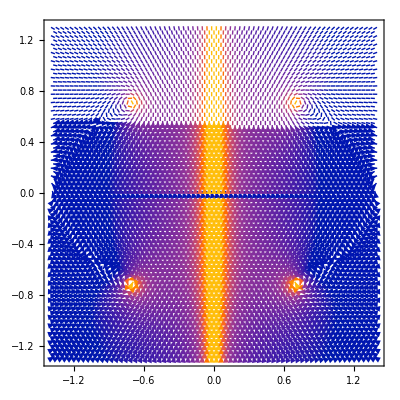

```mathematica
m=(3π)/12;
zp=1.4;
VectorPlot[2*{B[0,y,z,1,π/2-m][[2]],B[0,y,z,1,π/2-m][[3]]},{y,-zp,zp},{z,-zp^2/1.5,zp^2/1.5},VectorPoints->70]
```